```mathematica
(* 
θ is the phase = k.x-ω t 
ϕ is the polarizer angle
*)
```

## 2 perpendicular Polarization

```mathematica
EP={E1 Cos[θ], E2 Cos[θ]}.{Cos[ϕ],Sin[ϕ]}
```

E1 Cos[θ] Cos[ϕ]+E2 Cos[θ] Sin[ϕ]

```mathematica
Ii=EP^2
```

(E1 Cos[θ] Cos[ϕ]+E2 Cos[θ] Sin[ϕ])^2

```mathematica
∫_0^(2 π) Iiⅆθ
```

π (E1 Cos[ϕ]+E2 Sin[ϕ])^2

```mathematica
Manipulate[Plot[(E1 Cos[ϕ]+E2 Sin[ϕ])^2,{ϕ,0,π},PlotRange->{0,1}],{E1,0,1},{E2,0,1}]
```

## 2 perpendicular not in - phase

```mathematica
EP={E1 Cos[θ], E2 Cos[θ+δ]}.{Cos[ϕ],Sin[ϕ]}
```

E1 Cos[θ] Cos[ϕ]+E2 Cos[δ+θ] Sin[ϕ]

```mathematica
Ii=EP^2//Expand
```

E1^2 Cos[θ]^2 Cos[ϕ]^2+2 E1 E2 Cos[θ] Cos[δ+θ] Cos[ϕ] Sin[ϕ]+E2^2 Cos[δ+θ]^2 Sin[ϕ]^2

```mathematica
∫_0^(2 π) 2 E1 E2 Cos[θ] Cos[δ+θ] Cos[ϕ] Sin[ϕ]ⅆθ
```

E1 E2 π Cos[δ] Sin[2 ϕ]

```mathematica
II=∫_0^(2 π) Iiⅆθ
```

1/2 π (E1^2+E2^2+(E1^2-E2^2) Cos[2 ϕ]+4 E1 E2 Cos[δ] Cos[ϕ] Sin[ϕ])

```mathematica
Manipulate[Plot[E1 E2 Cos[δ] Sin[2 ϕ]+ E1^2  Cos[ϕ]^2+ E2^2  Sin[ϕ]^2,{ϕ,0,π},PlotRange->{0,1}],{E1,0,1},{E2,0,1},{δ,-π,π}]
```

## Multi - Linear || Same as 2-perp

```mathematica
(* Assume Any Scatter Ligth Can be Reduced to 2 perp. wave sources *)
```

Numerical Prove

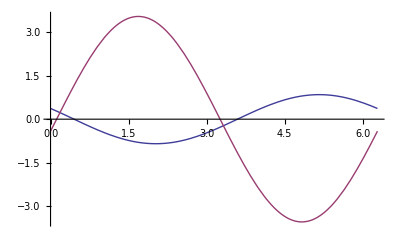

```mathematica
T=Table[Random[Real,{0,2}],{i,20}];
P=Table[Random[Real,{0,2π}],{i,20}];
A=Sum[T[[i]]Cos[T[[i]]]Cos[P[[i]]+θ],{i,20}];
B=Sum[T[[i]]Sin[T[[i]]]Cos[P[[i]]+θ],{i,20}];
Plot[{A,B},{θ,0,2 π}]
```

```mathematica
NSA=θ/.NSolve[A==0,θ][[2]]
NSB=θ/.NSolve[B==0,θ][[2]]
2(NSA-NSB)/π
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.451374

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.116941

0.212907

```mathematica
MA=FindMaximum[A,{θ,π}][[1]]
MB=FindMaximum[B,{θ,π}][[1]]
```

0.845907

FindMaximum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

3.54246

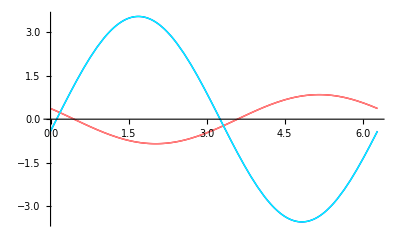

```mathematica
Plot[{A,B,MA Cos[θ-NSA+π/2],MB Sin[θ-NSB]},{θ,0,2π},PlotStyle->{Red,Blue,Pink,Cyan}]
```

Sum of Cosine = Cosine

```mathematica
A Cos[θ+α]+B Cos[θ+β]=Z Cos[θ+ζ]
```

```mathematica
A Cos[θ]Cos[α]-A Sin[θ]Sin[α]
+B Cos[θ]Cos[β]- B Sin[θ]Sin[β]=Z Cos[θ+ζ]
```

```mathematica
Cos[θ] (A Cos[α]+B Cos[β])
- Sin[θ](A Sin[α]+B Sin[β])=Z Cos[θ]Cos[ζ]-Z Sin[θ]Sin[ζ]
```

```mathematica
A Cos[α]+B Cos[β]=Z Cos[ζ]
A Sin[α]+B Sin[β]=Z Sin[ζ]
```

```mathematica
Z=√(A^2+B^2+2AB Cos[α-β])>0
Tan[ζ]=(A Sin[α]+B Sin[β])/(A Cos[α]+B Cos[β])
```

Sum of Sine = Sine

```mathematica
A Sin[θ+α]+B Sin[θ+β]=Z Sin[θ+ζ]
```

```mathematica
A Sin[θ]Cos[α]+A Sin[α]Cos[θ]
+B Sin[θ]Cos[β]+B Sin[β]Cos[θ]=Z Sin[θ+ζ]
```

```mathematica
Sin[θ](A Cos[α]+B Cos[β])
+Cos[θ](A Sin[α]+B Sin[β])=Z Sin[θ]Cos[ζ]+Z Sin[ζ]Cos[θ]
```

```mathematica
A Cos[α]+B Cos[β]=Z Cos[ζ]
A Sin[α]+B Sin[β]=Z Sin[ζ]
```

```mathematica
Z=√(A^2+B^2+2AB Cos[α-β])>0
Tan[ζ]=(A Sin[α]+B Sin[β])/(A Cos[α]+B Cos[β])
```

Math

```mathematica
E=Sum[{Ei Cos[αi]Cos[θ+βi],Ei Sin[αi] Cos[θ+βi]},{i,100}]
```

```mathematica
Ei Cos[αi]Cos[θ+βi]
=Ei/2( Cos[θ+βi+αi]+Cos[θ+βi-αi])
=E1 Cos [θ+ζ1]
```

```mathematica
Ei Sin[αi]Cos[θ+βi]
=Ei/2(Sin[θ+βi+αi]-Sin[θ+βi-αi])
=E2 Sin[θ+ζ2]
```

```mathematica
EP={E1  Cos[θ+ζ1], E2 Sin[θ+ζ2]}.{Cos[ϕ],Sin[ϕ]}
```

E1 Cos[ζ1+θ] Cos[ϕ]+E2 Sin[ζ2+θ] Sin[ϕ]

```mathematica
Li=EP^2
```

(E1 Cos[ζ1+θ] Cos[ϕ]+E2 Sin[ζ2+θ] Sin[ϕ])^2

```mathematica
∫_0^(2 π) Liⅆθ
```

1/2 π (E1^2+E2^2+(E1^2-E2^2) Cos[2 ϕ]-2 E1 E2 Sin[ζ1-ζ2] Sin[2 ϕ])

## Elliptical

```mathematica
EP={E1 Cos[θ], E2 Sin[θ]}.{Cos[ϕ],Sin[ϕ]}
```

E1 Cos[θ] Cos[ϕ]+E2 Sin[θ] Sin[ϕ]

```mathematica
Li=EP^2
```

(E1 Cos[θ] Cos[ϕ]+E2 Sin[θ] Sin[ϕ])^2

```mathematica
∫_0^(2 π) Liⅆθ
```

1/2 π (E1^2+E2^2+(E1^2-E2^2) Cos[2 ϕ])